```mathematica
WW11={{1.5,0},{1.6,0.2483358535585939},{1.7000000000000002,0.39415449657148244},{1.8000000000000003,0.49558333690312023},{1.9000000000000004,0.6077656364639598},{2.0000000000000004,0.7051933173131911},{2.05,0.6744583266777819},{2.0599999999999996,0.6551928977953217},{2.0699999999999994,0.7167646106942468},{2.079999999999999,0.7977986727128236},{2.089999999999999,0.6722090548030591},{2.11,0.7230537624061025},{2.1500000000000005,0.6700977267055457},{2.2000000000000006,0.7972428584761548},{2.3000000000000007,0.7052017832918375},{2.400000000000001,0.8435497519545393},{2.500000000000001,0.7924093538014908},{2.600000000000001,0.8357538787448574},{2.700000000000001,0.7647891374312247},{2.800000000000001,0.7549686055024432},{2.9,0.7329140724184086},{3,0.7126941610105193}};
```

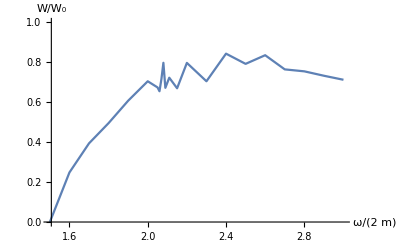

```mathematica
ListLinePlot[Re[WW11],PlotRange->{{1.5,3},{0,1}},AxesLabel->{ω/(2m),W/Subscript[W, 0]}]
```

```mathematica
StandardForm[WW11]
```

{{1.5,0},{1.6,0.248336},{1.7,0.394154},{1.8,0.495583},{1.9,0.607766},{2.,0.705193},{2.05,0.674458},{2.06,0.655193},{2.07,0.716765},{2.08,0.797799},{2.09,0.672209},{2.11,0.723054},{2.15,0.670098},{2.2,0.797243},{2.3,0.705202},{2.4,0.84355},{2.5,0.792409},{2.6,0.835754},{2.7,0.764789},{2.8,0.754969},{2.9,0.732914},{3,0.712694}}

```mathematica
fit0=FindFit[WW11,b0+b1 x+b2 x^2+b3 x^3+b4 x^4+b5 x^5+b6 x^6,{b0,b1,b2,b3,b4,b5,b6},x]
```

{b0→58.1868,b1→-204.852,b2→275.871,b3→-187.646,b4→69.2851,b5→-13.2868,b6→1.03878}

```mathematica
RR00[x_]:=Evaluate[b0+b1 x+b2 x^2+b3 x^3+b4 x^4+b5 x^5+b6 x^6/.fit0];
```

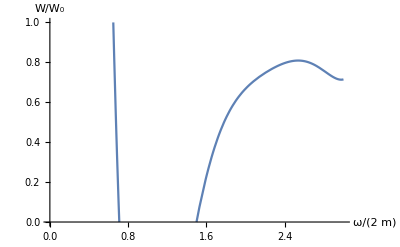

```mathematica
Plot[RR00[x],{x,0,3},PlotRange->{{0,3},{0,1}},AxesLabel->{ω/(2m),W/Subscript[W, 0]}]
```

```mathematica
RR00[2]
```

19.6678